# Funcs

```mathematica
plotIxnParams[dir_,param_,timepoint_]:=Module[
{dirI,data,maxTime,range,rangeMin,rangeMax},
SetDirectory[NotebookDirectory[]];
dirI="../data/"<>dir<>"/ixn_params/";
data=Import[dirI<>param<>"_"<>IntegerString[timepoint,10,5]<>".txt","Table"];
maxTime=data[[-1,1]];
rangeMin=IntegerPart[10*Min[data[[;;,2]]]]/10.0;
rangeMax=IntegerPart[10*Max[data[[;;,2]]]]/10.0;
rangeMin-=0.1;
rangeMax+=0.1;
range={rangeMin,rangeMax};
Return[ListLinePlot[data,
PlotRange->{{0,maxTime},range},
ImageSize->150
]];
];
```

```mathematica
getIxnParams[dir_,param_,timepoint_]:=Module[
{dirI,data,maxTime,range,rangeMin,rangeMax},
SetDirectory[NotebookDirectory[]];
dirI="../data/"<>dir<>"/ixn_params/";
data=Import[dirI<>param<>"_"<>IntegerString[timepoint,10,5]<>".txt","Table"];
Return[data];
];
```

```mathematica
plotIxnParams[dir_,param_,timepoint1_,timepoint2_]:=Module[
{dirI,data1,data2,maxTime,range,rangeMin,rangeMax},
SetDirectory[NotebookDirectory[]];
dirI="../data/"<>dir<>"/ixn_params/";
data1=Import[dirI<>param<>"_"<>IntegerString[timepoint1,10,5]<>".txt","Table"];
data2=Import[dirI<>param<>"_"<>IntegerString[timepoint2,10,5]<>".txt","Table"];
Return[ListLinePlot[{data1,data2},
PlotRange->All,
ImageSize->150
]];
];
```

```mathematica
plotIxnParams3D[dir_,timepoint_]:=Module[
{dirI,data1,data2,data3,range},
SetDirectory[NotebookDirectory[]];
dirI="../data/"<>dir<>"/ixn_params/";
data1=Import[dirI<>"hA_"<>IntegerString[timepoint,10,5]<>".txt","Table"][[;;,2]];
data2=Import[dirI<>"hB_"<>IntegerString[timepoint,10,5]<>".txt","Table"][[;;,2]];
data3=Import[dirI<>"hC_"<>IntegerString[timepoint,10,5]<>".txt","Table"][[;;,2]];
Return[ListPointPlot3D[Transpose[{data1,data2,data3}],
PlotRange->{{Min[data1],Max[data1]},{Min[data2],Max[data2]},{Min[data3],Max[data3]}},
ImageSize->500
]];
];
```

```mathematica
plotAdjoints[param_,timepoint_]:=Module[
{maxTime,range,dirA,dataA},
SetDirectory[NotebookDirectory[]];

dirA="../data/learn/adjoints/";
dataA=Import[dirA<>param<>"_"<>IntegerString[timepoint,10,4]<>".txt","Table"];
maxTime=dataA[[-1,1]];

range=Switch[param,
"hA",{-10,10},
"hB",{-10,10},
"hC",{-10,10},
"wAX1",{-10,10},
"wBX1",{-10,10},
"wCX1",{-10,10},
"bX1",{-10,10},
"wX1X2",{-10,10},
"bX2",{-10,10}
];
Return[ListLinePlot[{dataA},
PlotRange->{{0,20},range},
ImageSize->200
]];
];
```

# 1 hidden layer

```mathematica
plotIxnParams3D["learn_sequential",10000]
```

-Graphics3D-

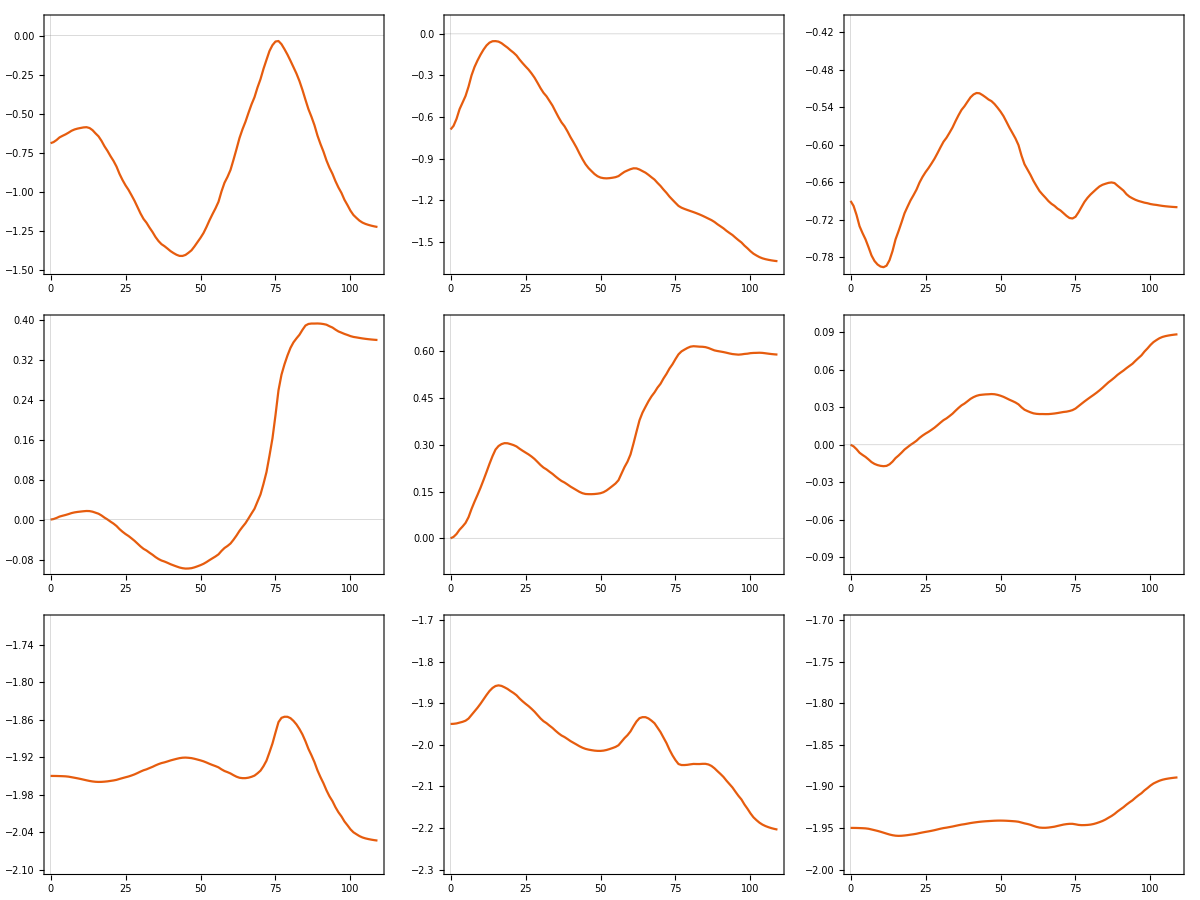

```mathematica
t=10000;
dirA="learn_sequential";
Grid[{{plotIxnParams[dirA,"hA",t],plotIxnParams[dirA,"hB",t],plotIxnParams[dirA,"hC",t]
},{plotIxnParams[dirA,"wAX1",t],plotIxnParams[dirA,"wBY1",t],plotIxnParams[dirA,"wCZ1",t]
},{plotIxnParams[dirA,"bX1",t],plotIxnParams[dirA,"bY1",t],plotIxnParams[dirA,"bZ1",t]
}}]
```

### Two times at once, for comparison

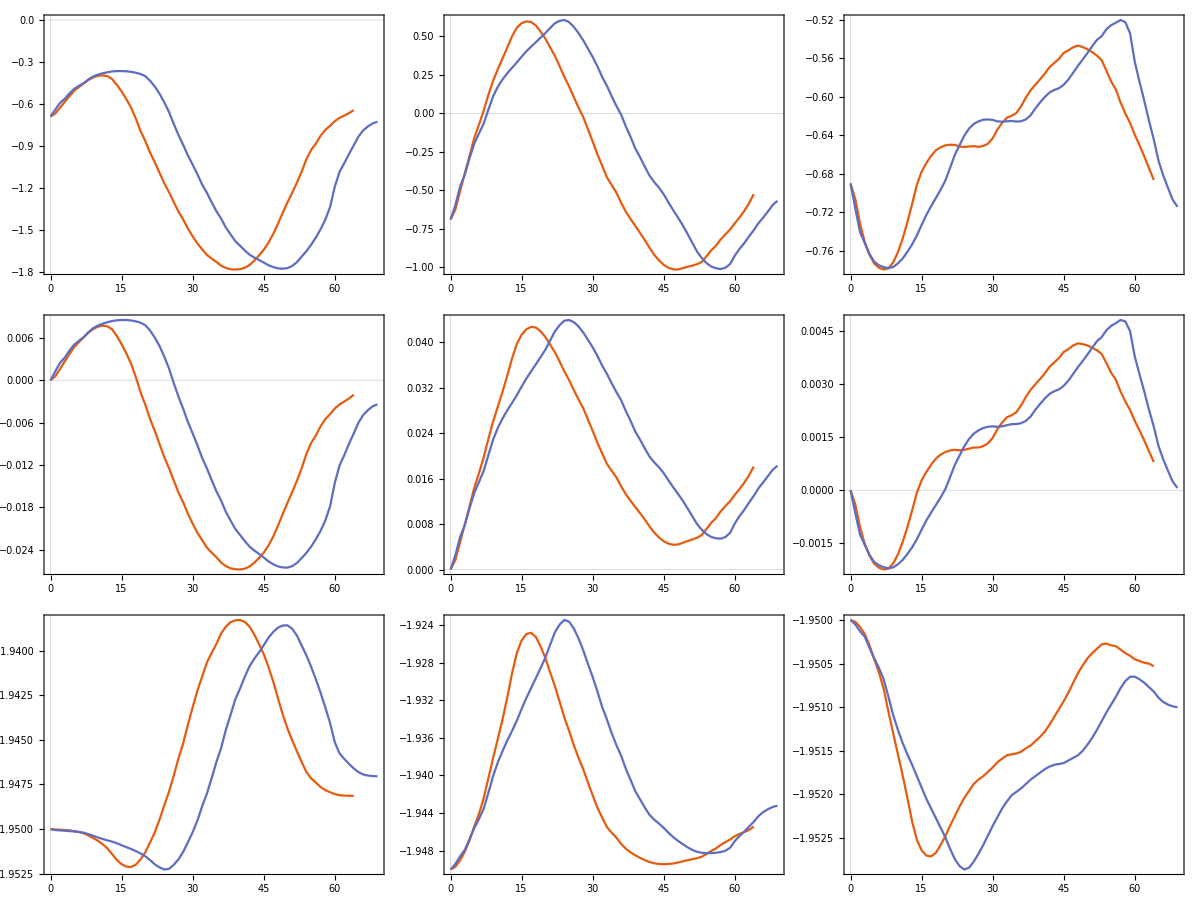

```mathematica
t1=5500;
t2=6000;
dirA="learn_sequential";
Grid[{{plotIxnParams[dirA,"hA",t1,t2],plotIxnParams[dirA,"hB",t1,t2],plotIxnParams[dirA,"hC",t1,t2]
},{plotIxnParams[dirA,"wAX1",t1,t2],plotIxnParams[dirA,"wBY1",t1,t2],plotIxnParams[dirA,"wCZ1",t1,t2]
},{plotIxnParams[dirA,"bX1",t1,t2],plotIxnParams[dirA,"bY1",t1,t2],plotIxnParams[dirA,"bZ1",t1,t2]
}}]
```

# Legacy: 1 hidden layer full

```mathematica
plotIxnParams3D["learn_sequential_f",1600]
```

-Graphics3D-

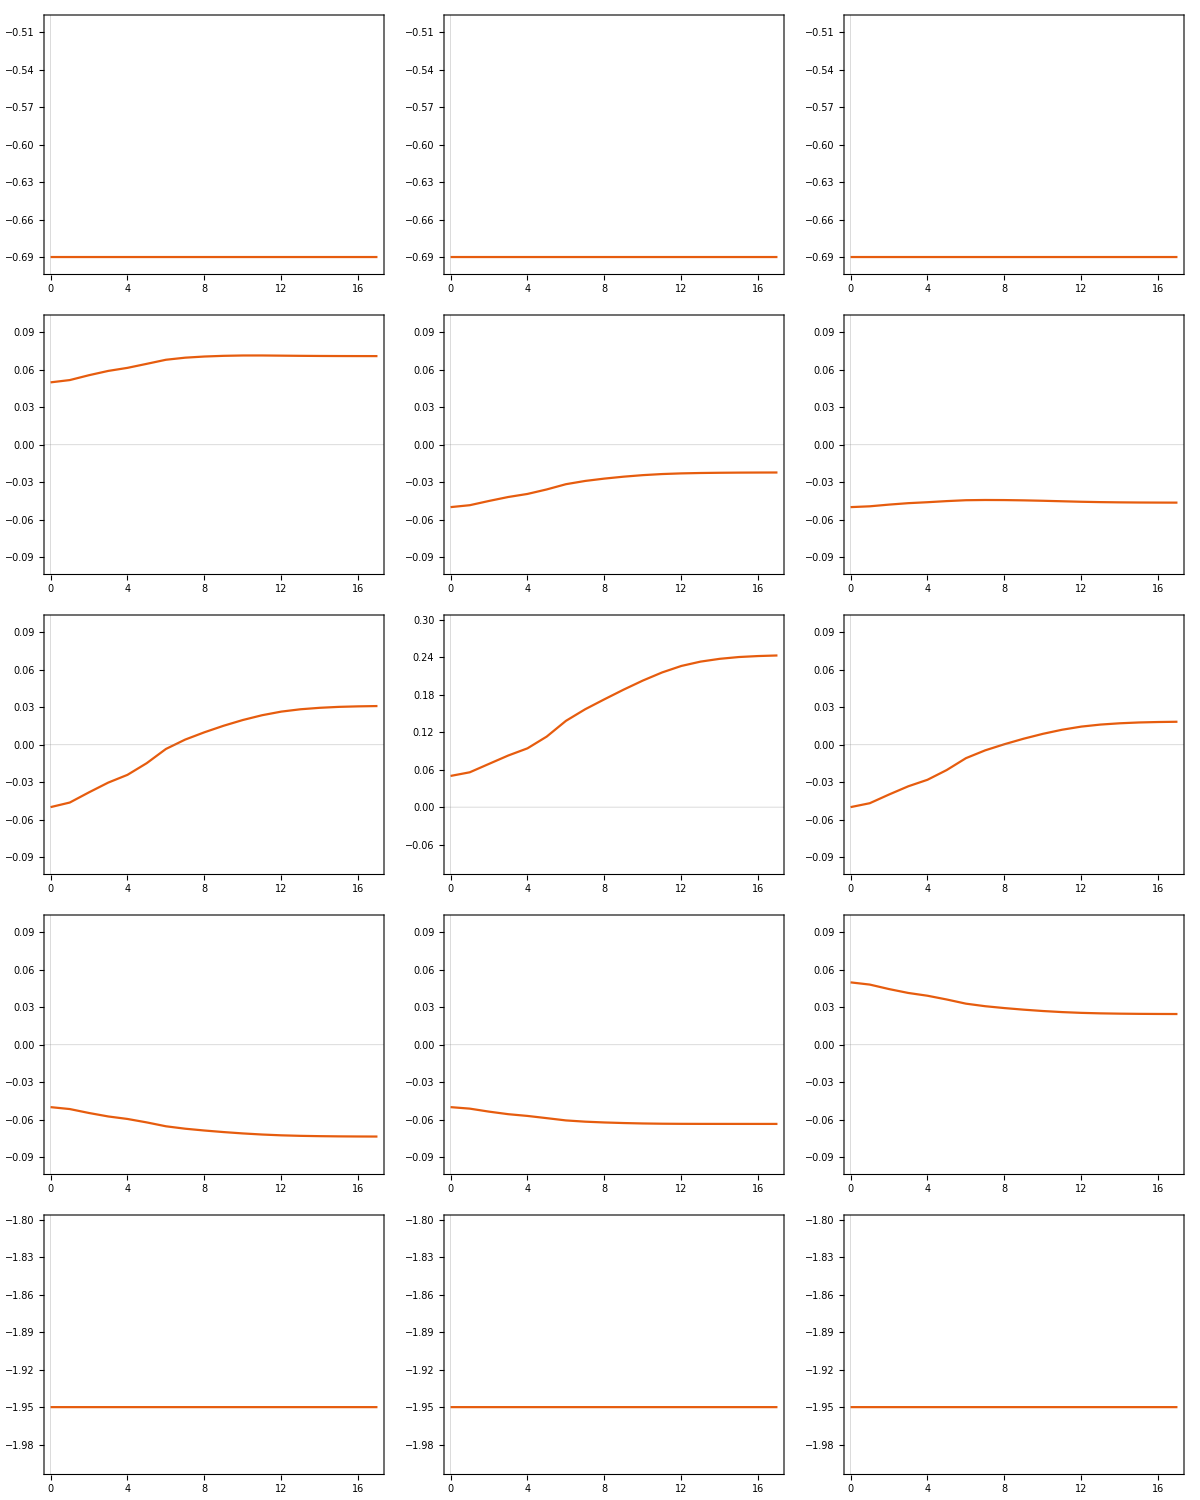

```mathematica
t=800;
dirA="learn_sequential_f";
Grid[{{plotIxnParams[dirA,"hA",t],plotIxnParams[dirA,"hB",t],plotIxnParams[dirA,"hC",t]
},{plotIxnParams[dirA,"wAX1",t],plotIxnParams[dirA,"wAY1",t],plotIxnParams[dirA,"wAZ1",t]
},{plotIxnParams[dirA,"wBX1",t],plotIxnParams[dirA,"wBY1",t],plotIxnParams[dirA,"wBZ1",t]
},{plotIxnParams[dirA,"wCX1",t],plotIxnParams[dirA,"wCY1",t],plotIxnParams[dirA,"wCZ1",t]
},{plotIxnParams[dirA,"bX1",t],plotIxnParams[dirA,"bY1",t],plotIxnParams[dirA,"bZ1",t]
}}]
```

# Legacy: 2 hidden layers

```mathematica
dirA="learn_traj_2layers";
t=750;
mTime=15;
Grid[{{plotIxnParams[dirA,"hA",t,mTime],plotIxnParams[dirA,"hB",t,mTime],plotIxnParams[dirA,"hC",t,mTime]
},{plotIxnParams[dirA,"wAX1",t,mTime],plotIxnParams[dirA,"wBY1",t,mTime],plotIxnParams[dirA,"wCZ1",t,mTime]
},{plotIxnParams[dirA,"bX1",t,mTime],plotIxnParams[dirA,"bY1",t,mTime],plotIxnParams[dirA,"bZ1",t,mTime]
},{plotIxnParams[dirA,"wX1X2",t,mTime],plotIxnParams[dirA,"wY1Y2",t,mTime],plotIxnParams[dirA,"wZ1Z2",t,mTime]
},{plotIxnParams[dirA,"bX2",t,mTime],plotIxnParams[dirA,"bY2",t,mTime],plotIxnParams[dirA,"bZ2",t,mTime]
}}]
```

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦-1,1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

System`ListPlotsDump`messageshead$339414::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::sfunc: {{Identity,Identity},{Identity,Identity}} is not a valid scaling function.

System`ListPlotsDump`messageshead$339461::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::sfunc: {{Identity,Identity},{Identity,Identity}} is not a valid scaling function.

System`ListPlotsDump`messageshead$339498::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::sfunc: {{Identity,Identity},{Identity,Identity}} is not a valid scaling function.

General::stop: Further output of General::sfunc will be suppressed during this calculation.

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦-1,1⟧ is longer than depth of object.

System`ListPlotsDump`messageshead$339552::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$339587::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$339620::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Import::nffil: File not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦-1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

System`ListPlotsDump`messageshead$339668::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$339705::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$339738::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$339778::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$339809::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$339842::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$339878::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$339926::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$339965::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340003::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340034::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340069::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340109::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340140::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340175::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340213::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340244::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340277::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340317::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340348::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340381::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340421::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340454::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340487::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340525::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340556::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340589::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340629::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340662::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340693::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340733::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340766::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340797::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340837::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340868::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$340903::prng: Value of option PlotRange -> {{0,15},{IntegerPart[Symbol[]],IntegerPart[Symbol[]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

$Aborted

```mathematica
s
```

```mathematica
Manipulate[
Grid[{{
plotAdjoints["hA",t],
plotAdjoints["hB",t],
plotAdjoints["hC",t]
},{
plotAdjoints["wAX1",t],
plotAdjoints["wBX1",t],
plotAdjoints["wCX1",t]
},{
plotAdjoints["bX1",t],
plotAdjoints["wX1X2",t],
plotAdjoints["bX2",t]
}}]
,{t,0,240,1}]
```

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦-1,1⟧ is longer than depth of object.

System`ListPlotsDump`messageshead$930028::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-10,10}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦-1,1⟧ is longer than depth of object.

System`ListPlotsDump`messageshead$930087::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-10,10}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Import::nffil: File not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦-1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

System`ListPlotsDump`messageshead$930150::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-10,10}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$930203::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-10,10}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$930252::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-10,10}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$930301::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-10,10}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$930350::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-10,10}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$930399::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-10,10}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$930448::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-10,10}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$16807::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-1.5,-0.6}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$16842::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-1.5,-0.6}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$16876::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-1.5,-0.6}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$16915::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-0.4,0.4}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$16948::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-0.4,0.4}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$16981::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-0.4,0.4}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$17018::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-0.4,0.8}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$17051::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-0.4,0.8}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$17084::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-0.4,0.8}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$17121::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-0.4,0.4}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$17154::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-0.4,0.4}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$17187::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-0.4,0.4}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$17224::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-3.,-0.5}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$17255::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-3.,-0.5}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$17290::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-3.,-0.5}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$17327::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-0.4,0.4}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$17360::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-0.4,0.4}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$17393::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-0.4,0.4}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$17430::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-2.,0.}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$17463::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-2.,0.}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

System`ListPlotsDump`messageshead$17494::prng: Value of option PlotRange -> {{0,$Failed⟦-1,1⟧},{-2.,0.}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.